```mathematica
Answers to Exercises   Kai Shen (10157891)
```

```mathematica
Week 3
```

```mathematica
Q1
checkEulerT[x_,y_]:=(Print[GCD[x,y]];Print[EulerPhi[x]];Mod[y^EulerPhi[x],x])
Prime[100000]
checkEulerT[Prime[100000],11111]
1299709
1
1299709
1
checkEulerT[3,8]
1
2
1
Q2-----------------------------------
ExtendedGCD[Prime[200],Prime[201]]
{1,{-205,204}}
Prime[200]*(-205)+Prime[201]*204
1
Q3----------------------------
u1=ChineseRemainder[{1,0,0},{13,29,64}]
7424
u2=ChineseRemainder[{0,1,0},{13,29,64}]
13312
u3=ChineseRemainder[{0,0,1},{13,29,64}]
3393
u1*10+u2*5+u3*7-13*29*64*6
19783
ChineseRemainder[{10,5,7},{13,29,64}]
19783
Q4----------------------------
cA=PowerMod[57766,56,Prime[10000]]
cB=PowerMod[57766,111,Prime[10000]]
30255
24601
PowerMod[cB,56,Prime[10000]]
42897
PowerMod[cA,111,Prime[10000]]
42897
Q5------------------------
mB=167
p=Prime[197];a=2;cB=PowerMod[a,mB,p];r=RandomInteger[{0,p-2}]
u=456;R=PowerMod[a,r,p]
S=Mod[PowerMod[cB,r,p] u,p]
Mod[S*PowerMod[PowerMod[R,mB,p],-1,p],p]
167
298
901
959
456
Q6------------------------
p=Prime[197];a=2;mA=376;r=Prime[100];u=456;S=.;R=PowerMod[a,r,p]
S=S/.Solve[{r *S==u-mA *R},{S},Modulus->p-1][[1]]
cA=PowerMod[a,mA,p];
PowerMod[a,u,p]==Mod[ PowerMod[cA,R,p]*PowerMod[R,S,p],p]
210
456
True
Q7--------------------------------
pB=Prime[1300]
qB=Prime[1450]
nB=pB*qB
phiB=EulerPhi[nB]
eB=RandomInteger[{1,nB}];
While[GCD[eB,phiB]≠1,eB=RandomInteger[{1,nB}]];
{x1,{dB,x3}}=ExtendedGCD[eB,phiB]
Mod[eB*dB,phiB]
m=12345678;
c=PowerMod[m,eB,nB]
PowerMod[c,dB,nB]


10657
12109
129045613
129022848
{1,{-23430431,8335433}}
1
97764043
12345678
Q8------------------------
pB1=Prime[1300]
qB1=Prime[1450]
nB1=pB1*qB1
phiB1=EulerPhi[nB1]
eB1=RandomInteger[{1,nB1}];
While[GCD[eB1,phiB1]≠1,eB1=RandomInteger[{1,nB1}]];
{x1,{dB1,x3}}=ExtendedGCD[eB1,phiB1]
Mod[eB1*dB1,phiB1]
pB2=Prime[1301]
qB2=Prime[1451]
nB2=pB2*qB2
phiB2=EulerPhi[nB2]
eB2=RandomInteger[{1,nB2}];
While[GCD[eB2,phiB2]≠1,eB2=RandomInteger[{1,nB2}]];
{x1,{dB2,x3}}=ExtendedGCD[eB2,phiB2]
Mod[eB2*dB2,phiB2]
m=12345678;
c=PowerMod[PowerMod[m,eB1,nB1],dB2,nB2]
PowerMod[PowerMod[c,eB2,nB2],dB1,nB1]

10657
12109
129045613
129022848
{1,{-7624871,6624051}}
1
10663
12113
129160919
129138144
{1,{53045,-40291}}
1
66490829
12345678
```

```mathematica
Week 4
```

Q1

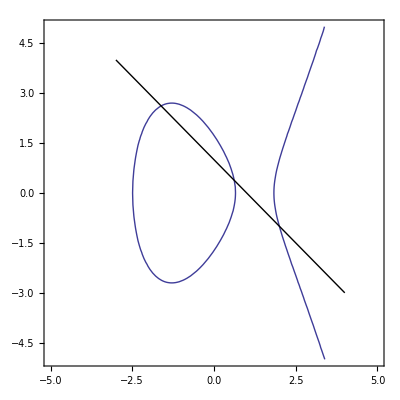

```mathematica
Q1


elliptic=ContourPlot[y^2==x^3-5 x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]]
```

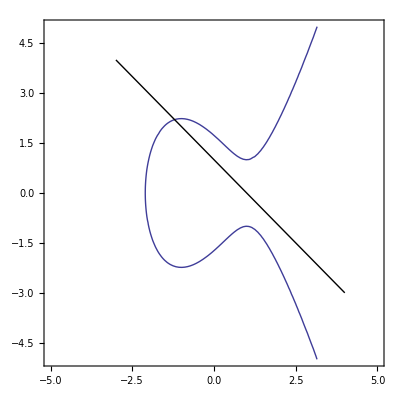

```mathematica
elliptic=ContourPlot[y^2==x^3-3x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]]
```

```mathematica
Q2
```

```mathematica
Manipulate[ContourPlot[y^2==x^3+n*x+3,{x,-5,5},{y,-5,5},Axes->True,Epilog->Line[{{-3,4},{4,-3}}]],{n,-5,-3,1}]

The straight line  intersects elliptic curves in only one place. When the coefficient of x is -3.
```

```mathematica
Q3
```

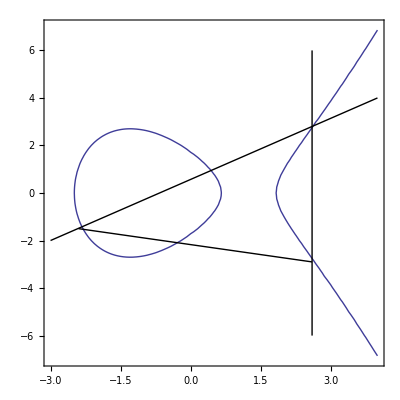

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x+3,{x, -3,4},{y,-7,7},Axes->True,Epilog->{Line[{{2.6,6},{2.6,-6}}],Line[{{-3,-2},{4,4}}],Line[{{-2.4,-1.5},{2.6,-2.9}}]}]
```

```mathematica
{2.6,-2.9}
```

```mathematica
Q4
```

```mathematica
Clear[x,y]; 
p=11;
Table[ Solve[ {y^2== x^3-5 x + 3, x==u},{x,y}, Modulus->p], {u, 0, p-1}]
```

{{{x→0,y→5},{x→0,y→6}},{},{{x→2,y→1},{x→2,y→10}},{{x→3,y→2},{x→3,y→9}},{{x→4,y→5},{x→4,y→6}},{{x→5,y→2},{x→5,y→9}},{},{{x→7,y→5},{x→7,y→6}},{},{{x→9,y→4},{x→9,y→7}},{}}

```mathematica
Q5
```

```mathematica
InterpolatingPolynomial[{{0,5},{2,10}},v1]
```

5+(5 v1)/2

```mathematica
p=11;Solve[ {y^2==x^3-5 x+3,y==5+(5 x)/2},{x,y},Modulus-> p]
```

{{x→0,y→5},{x→2,y→10},{x→7,y→6}}

```mathematica
Q6
```

```mathematica
EllipticAdd[11,0,-5,3,{0,5},{2,10}]
```

{7,5}

```mathematica
vertical coordinates addtion inverse each other
5+6=11=0mod p
```

```mathematica
Q7
```

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
```

```mathematica
Table[P[n],{n,10,20,1}]
```

{{533,612},{579,214},{790,469},{348,20},{539,396},{572,41},{124,665},{804,720},{363,491},{533,251},{579,649}}

```mathematica
IntegerDigits[432,2]
```

```mathematica
{1,1,0,1,1,0,0,0,0}
```

```mathematica
IntegerDigits[432,2]
```

{1,1,0,1,1,0,0,0,0}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
```

{O}

```mathematica
Q8
```

```mathematica
{539,396}
```

```mathematica
p=863;a=100;b=10;c=1;x=539;y=396;Mod[y^2-(x^3+a*x^2+b*x+c),p]==0
```

True

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={539,396};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];		 
QAlice=EllipticAdd[p,a,b,c,P[7],P[5]]
QBob=EllipticAdd[p,a,b,c,P[8],P[5]]
QA[0]=QBob;QA[i_]:=QA[i]=EllipticAdd[p,a,b,c,QA[i-1],QA[i-1]];EllipticAdd[p,a,b,c,QA[7],QA[5]]
QB[0]=QAlice;QB[i_]:=QB[i]=EllipticAdd[p,a,b,c,QB[i-1],QB[i-1]];EllipticAdd[p,a,b,c,QB[8],QB[5]]
```

{533,612}

{341,688}

{341,688}

{341,688}

```mathematica
Q9
```

```mathematica
dd+dd
```

0

```mathematica
dd-dd
```

0

```mathematica
dd+ee
```

{1,1,1,1}_2

```mathematica
dd-ee
```

{1,1,1,1}_2

```mathematica
Table[dd^n,{n,0,15,1}]
```

{1,{0,0,1,1}_2,{0,1,1,0}_2,{1,1,0,0}_2,{1,0,1,1}_2,{0,1,0,1}_2,{1,0,1,0}_2,{0,1,1,1}_2,{1,1,1,0}_2,{1,1,1,1}_2,{1,1,0,1}_2,{1,0,0,1}_2,{0,0,0,1}_2,{0,0,1,0}_2,{0,1,0,0}_2,{1,0,0,0}_2}

```mathematica
Q10
```

```mathematica
Table[(dd^n)^3+ee*(dd^n)^2,{n,0,15,1}]
```

{{0,1,0,0}_2,{1,0,0,1}_2,{1,1,0,1}_2,0,{1,0,0,0}_2,{1,0,1,0}_2,{0,1,0,0}_2,{1,1,0,0}_2,{0,1,0,0}_2,{1,0,1,1}_2,{0,1,1,0}_2,{0,0,0,1}_2,{1,0,1,1}_2,{1,0,1,1}_2,{0,0,1,0}_2,{0,1,0,0}_2}

```mathematica
(dd^3)^3+ee*(dd^3)^2
```

0

```mathematica
x=dd^3
Subscript[{1,1,0,0}, 2]
y=x
Subscript[{1,1,0,0}, 2]
a=ee;c=0;
P[0]={x,y};
P[i_] := P[i] = Z2mEllipticAdd[a,c,P[i-1],P[i-1]];
```

```mathematica
PDoubles=Table[P[n],{n,0,31,1}]
```

{{{1,1,0,0}_2,{1,1,0,0}_2},{{1,0,1,0}_2,{0,1,0,1}_2},{{0,0,0,1}_2,{0,1,0,1}_2},{{1,1,1,1}_2,{1,1,0,0}_2},{{1,1,0,0}_2,0},{{1,0,1,0}_2,{1,1,1,1}_2},{{0,0,0,1}_2,{0,1,0,0}_2},{{1,1,1,1}_2,{0,0,1,1}_2},{{1,1,0,0}_2,{1,1,0,0}_2},{{1,0,1,0}_2,{0,1,0,1}_2},{{0,0,0,1}_2,{0,1,0,1}_2},{{1,1,1,1}_2,{1,1,0,0}_2},{{1,1,0,0}_2,0},{{1,0,1,0}_2,{1,1,1,1}_2},{{0,0,0,1}_2,{0,1,0,0}_2},{{1,1,1,1}_2,{0,0,1,1}_2},{{1,1,0,0}_2,{1,1,0,0}_2},{{1,0,1,0}_2,{0,1,0,1}_2},{{0,0,0,1}_2,{0,1,0,1}_2},{{1,1,1,1}_2,{1,1,0,0}_2},{{1,1,0,0}_2,0},{{1,0,1,0}_2,{1,1,1,1}_2},{{0,0,0,1}_2,{0,1,0,0}_2},{{1,1,1,1}_2,{0,0,1,1}_2},{{1,1,0,0}_2,{1,1,0,0}_2},{{1,0,1,0}_2,{0,1,0,1}_2},{{0,0,0,1}_2,{0,1,0,1}_2},{{1,1,1,1}_2,{1,1,0,0}_2},{{1,1,0,0}_2,0},{{1,0,1,0}_2,{1,1,1,1}_2},{{0,0,0,1}_2,{0,1,0,0}_2},{{1,1,1,1}_2,{0,0,1,1}_2}}

```mathematica
Q11
```

```mathematica
a=ee = z16[{1,1,0,0}];c=0;
x=dd^3
Subscript[{1,1,0,0}, 2]
y=x
P[0]={x,y};
P[i_] := P[i] = Z2mEllipticAdd[a,c,P[i-1],P[i-1]];		 
QAlice=Z2mEllipticAdd[a,c,P[3],P[1]]
QBob=Z2mEllipticAdd[a,c,P[4],P[2]]
```

{1,1,0,0}_2

{1,1,0,0}_2

{1,1,0,0}_2

{{0,0,1,0}_2,{1,1,0,1}_2}

{{1,0,0,1}_2,{0,0,0,1}_2}

```mathematica
P[3]
```

{{1,1,1,1}_2,{1,1,0,0}_2}

```mathematica
Clear[QA,QB]
```

```mathematica
QA[0]=QBob;
```

```mathematica
QA[i_]:=QA[i]=Z2mEllipticAdd[a,c,QA[i-1],QA[i-1]];
```

```mathematica
QA[0]=QBob;QA[i_]:=QA[i]=Z2mEllipticAdd[a,c,QA[i-1],QA[i-1]];Z2mEllipticAdd[a,c,QA[3],QA[1]]
```

{{0,0,0,1}_2,{0,1,0,0}_2}

```mathematica
QB[0]=QAlice;QB[i_]:=QB[i]=Z2mEllipticAdd[a,c,QB[i-1],QB[i-1]];Z2mEllipticAdd[a,c,QB[4],QB[2]]
```

{{0,0,0,1}_2,{0,1,0,0}_2}

```mathematica
Week 5
```

```mathematica
Q1
```

```mathematica
AliceBasis = Table[Random[Integer],{40}]
```

{0,1,0,1,1,0,0,0,1,1,0,0,1,1,1,1,0,1,0,0,1,0,0,1,1,1,1,0,0,0,0,0,1,1,0,0,1,1,1,0}

```mathematica
AliceData= Table[Random[Integer],{40}]
```

{0,0,0,0,0,0,1,0,0,1,1,0,0,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
BobBasis= Table[Random[Integer],{40}]
```

{0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,0,1,0,0,0,1,0,1,1,0,1,0,1,0,0,0,0,0,0}

```mathematica
BobData1[x_,y_,z_] :=(t=Table[Random[Integer],{40}];For[i=1,i<40,i++,If[x [[i]]== y[[i]],t[[i]]=z[[i]],Random[Integer]]];Return [t])
```

```mathematica
BobData=BobData1[AliceBasis,BobBasis,AliceData]
```

{1,1,1,0,0,0,1,0,1,0,0,0,1,1,0,0,1,0,0,0,0,1,1,1,1,0,0,1,0,1,0,1,1,1,1,1,0,1,0,1}

```mathematica
sameCheck[x_,y_] := (t=Table[Random[Integer],{40}];For[i=1,i<40,i++,If[x [[i]]== y[[i]],t[[i]]=1,0]];Return [t])
```

```mathematica
checksame = sameCheck[AliceBasis,BobBasis]
```

{1,0,1,1,1,0,0,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,0,0,0}

```mathematica
EqualBases[x_,y_]:=(t=Table[Random[Integer],{40}];For[i=1,i<41,i++,t[[i]]=If[x[[i]]==y[[i]
],1,0]];Return[t])
```

```mathematica
eb=EqualBases[AliceBasis,BobBasis]
```

{1,1,1,0,0,1,1,1,0,0,1,1,0,1,1,0,0,1,0,0,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,1,0,0,0,1}

```mathematica
AgreeSelect[x_,y_]:=(t={};For[i=1,i<40,i++,If[x[[i]]==1,t=Append[t,y[[i]]]]];t)
```

```mathematica
AgreeSelect[eb,AliceData]
```

{1,0,1,1,1,0,0,0,1,0,0,0,1,1,1,0,1,1,1}

```mathematica
t1={}
t2 ={}
For[i=1,i<40,i++,If[checksame[[i]]==1,If[Random[Integer]==1,t1=Append[t1,BobData[[i]]],t2=Append[t2,BobData[[i]]]]]];
```

```mathematica
AgreeKeyBob=t1
```

{1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,1,0,0,1,1}

```mathematica
CheckDigitBob=t2
```

{1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,0,0,1,1,1,0,1,0,1,1,0}

```mathematica
t1={}
t2 ={}
For[i=1,i<40,i++,If[checksame[[i]]==1,If[Random[Integer]==1,t1=Append[t1,AliceData[[i]]],t2=Append[t2,AliceData[[i]]]]]];
```

{}

{}

```mathematica
AgreeKeyAlice=t1
```

{1,0,1,0,0,1,0,0,1,1,1,0,0,0,1,1}

```mathematica
CheckDigitAlice =t2
```

{1,1,1,1,0,0,0,0,1,0,1,1,0}

```mathematica
Q2
```

```mathematica
AliceBasis = Table[Random[Integer],{40}]
```

{1,0,1,1,0,1,1,0,1,1,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,1,0,0,0,1}

```mathematica
AliceData=AliceBasis
```

{1,0,1,1,0,1,1,0,1,1,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,1,0,0,0,1}

```mathematica
BobBasis= Table[Random[Integer],{40}]
```

{1,1,1,0,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1,1,0,1,0,1,1,1}

```mathematica
BobData= Table[Random[Integer],{40}]
```

```mathematica
reliableData =Table[Random[Integer],{40}]
```

{1,1,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,0,0,1,0,0,1,0,1,1,1,1,0,0,1,0,0,1,1,0,0,1,0,1}

```mathematica
For[i=1,i<40,i++,
	If[AliceBasis [[i]] ==BobBasis[[i]],
		BobData[[i]] =AliceData[[i]];reliableData[[i]] =1 ,
		BobData[[i]] = Random[Integer];reliableData[[i]] =0
	]
]
```

```mathematica
BobData
```

{1,1,1,1,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,0,1,1,0,1,0,1,0,0,0,1}

```mathematica
reliableData
```

{1,0,1,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,1,1,1,0,1,1,0,1,0,0,1,0,0,1,0,1,0,1,1,0,0,1}

```mathematica
AgreeDataAlice= Table[Random[Integer],{40}]
```

{0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,1,0}

```mathematica
AgreeDataBob= Table[Random[Integer],{40}]
```

{0,1,0,1,1,0,1,1,1,0,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0}

```mathematica
For[i=1,i<40,i++,
	If[reliableData[[i]] ==1,
		AgreeDataAlice =Append[AgreeDataAlice,AliceData[[i]]];
		AgreeDataBob =Append[AgreeDataBob,AliceData[[i]]]
	]
]
```

```mathematica
AgreeDataAlice
```

{0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,0,0,1,1,0,0,1,1,1,0}

```mathematica
AgreeDataBob
```

{0,1,0,1,1,0,1,1,1,0,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,1,0,0,0,0,0,1,1,0,0,1,1,1,0}

```mathematica
For[i=1,i<40,i++,
	If[reliableData[[i]]==1,
		If[Random[Integer]==1,
			t1=Append[t1,BobData[[i]]],
			t2=Append[t2,BobData[[i]]]]]];
```

```mathematica
AgreeKeyBob = t1
```

{1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,1,1,0}

```mathematica
CheckdigitBob = t1
```

{1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,1,1,0}

```mathematica
t1 ={}
t2={}
```

{}

{}

```mathematica
For[i=1,i<40,i++,
	If[reliableData[[i]]==1,
		If[Random[Integer]==1,
			t1=Append[t1,AliceData[[i]]],
			t2=Append[t2,AliceData[[i]]]]]];
```

```mathematica
AgreeKeyAlice = t1
```

{1,0,0,0,0,0,1,1,0,0,1}

```mathematica
CheckdigitAlice = t2
```

{1,1,0,0,1,1,0}

```mathematica
Q3
```

```mathematica
BobBasis= Table[Random[Integer],{40}]
AliceBasis= Table[Random[Integer],{40}]
```

{0,1,0,0,1,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,0,1,1,0,0,0,0,1,0,1,1,1,1,0,0,1,1}

{0,0,0,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,0}

```mathematica
EqualBases= Table[Random[Integer],{40}]
For[i=1,i<40,i++,
	If[AliceBasis [[i]] ==BobBasis[[i]],
		EqualBases[[i]] =1 ,
		EqualBases[[i]] =0
	]
]
```

{0,0,0,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,0,0,0,0}

```mathematica
EqualBases
```

{1,0,1,0,1,0,0,0,0,0,1,0,0,1,0,0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,0,1,1,1,1,0,0,1,1,0}

```mathematica
EveDrops = Table[Random[Integer],{40}]
```

{0,0,1,1,1,1,0,0,0,1,0,1,0,0,0,1,1,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,0}

```mathematica
ReliableData=Table[Random[Integer],{40}]
```

{1,1,0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,0,0,0,1,1,0,0,1,0,1,0}

```mathematica
For[i=1,i<40,i++,
	If[EqualBases[[i]] ==1&&EveDrops[[i]]==0 ,
		ReliableData[[i]] =1 ,
		ReliableData[[i]] =0
	]
]
```

```mathematica
BobData= Table[Random[Integer],{40}]
AliceData= Table[Random[Integer],{40}]
For[i=1,i<40,i++,
	If[ReliableData[[i]] =1 ,
		BobData[[i]] =AliceData[[i]]
	]
]
```

```mathematica
BobData
AliceData
```

{0,0,0,1,1,1,1,0,1,0,1,1,0,0,1,0,0,0,1,0,1,0,0,0,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,1}

{0,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,1,1,1,0,0,1,0,0,1,1,0,0,0,1,1,1,1,1,0,1,0,1}

```mathematica
t1={}
t2={}
For[i=1,i<40,i++,
	If[EqualBases[[i]]==1,
			t1=Append[t1,AliceData[[i]]];
			t2=Append[t2,BobData[[i]]]
	]
]
```

{}

{}

```mathematica
AgreeDataBob = t2
AgreeDataAlice =t1
```

{0,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,0,0}

{0,1,0,0,0,1,1,1,0,0,1,0,1,1,1,1,1,0}

```mathematica
t1={}
t2={}
For[i=1,i<40,i++,
	If[ReliableData[[i]]==1,
		If[Random[Integer]==1,
			t1=Append[t1,AliceData[[i]]],
			t2=Append[t2,AliceData[[i]]]]]];
AgreeKeyAlice  = t1
CheckdigitAlice = t2
```

{}

{}

{0,0,1,0,0,1,1,0,1,0,1,1,0,1,0,0,1,1,1,1}

{0,1,0,1,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0}

```mathematica
t1={}
t2={}
For[i=1,i<40,i++,
	If[ReliableData[[i]]==1,
		If[Random[Integer]==1,
			t1=Append[t1,BobData[[i]]],
			t2=Append[t2,BobData[[i]]]]]];
AgreeKeyBob  = t1
CheckdigitBob = t2
```

{}

{}

{0,1,1,0,1,1,0,0,0,0,0,1,1,1,1,1,1,0,1,1,1,1,0}

{0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0}

```mathematica
Comments:There is great difference between agree keys and checkdigit, for that there are some measuring movements happen.
```